Melissa Lee
105-128-234
melissaloreleilee@gmail.com
HW 3

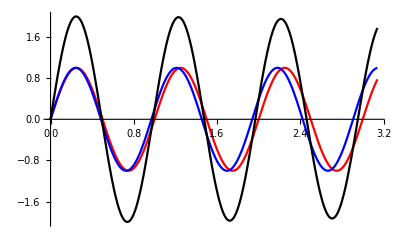

```mathematica
(*Problem 1*)
Remove["Global`*"]
(*eqations*)
y[1][x_,t_]=A1 Sin[k1 (x-v t)];
y[2][x_,t_]=A2 Sin[k2 (x+v t)];
y[r][x_,t_]=y[1][x,t]+y[2][x,t];
(*plug in variables*)
k2=k1+δk;
v=1;
k1=2 π;
A1=1;
A2=1;
δk=0.2;
(*Plot and Animate*)
Plot[{y[1][x,0],y[2][x,0],y[r][x,0]},{x,0,π},PlotStyle->{Red,Blue,Black}]
waveplot[t_]:= Plot[{y[1][x,t],y[2][x,t],y[r][x,t]},{x,0,20},PlotStyle->{Red,Blue,Black}]
Animate[waveplot[t],{t,0,50, 0.1}]
```

δk = 0.1

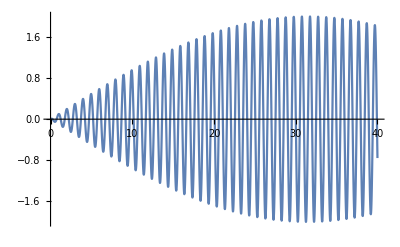

δk = 0.4

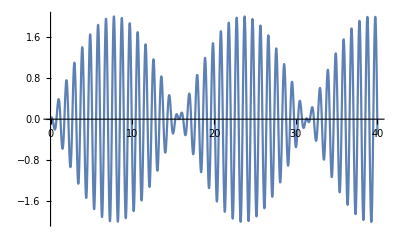

δk = 0.7

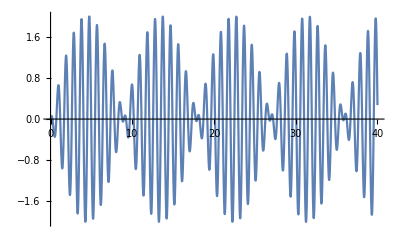

δk = 1.5

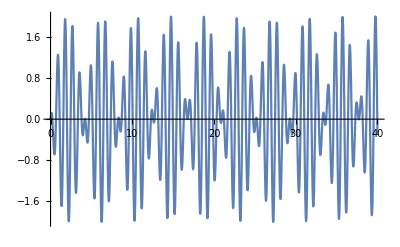

δk = 2.0

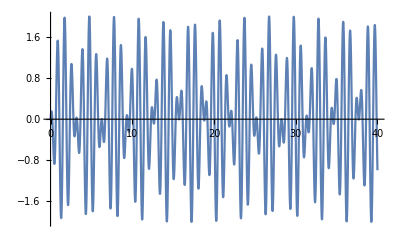

δk = 3.0

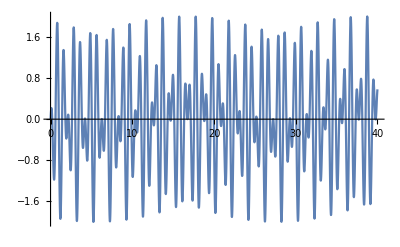

```mathematica
(*Problem 2 Part i*)
Remove["Global`*"]
(*eqations*)
y[1][x_,t_]=A1 Sin[k1 (x-v t)];
y[2][x_,t_]=A2 Sin[k2 (x+v t)];
y[r][x_,t_]=y[1][x,t]+y[2][x,t];
(*plug in variables*)
k2=k1+δk;
v=1;
k1=2 π;
A1=1;
A2=1;
Print["δk = 0.1"]
Plot[y[r][0,t]/.δk->0.1,{t,0,40}]
Print["δk = 0.4"]
Plot[y[r][0,t]/.δk->0.4,{t,0,40}]
Print["δk = 0.7"]
Plot[y[r][0,t]/.δk->0.7,{t,0,40}]
Print["δk = 1.5"]
Plot[y[r][0,t]/.δk->1.5,{t,0,40}]
Print["δk = 2.0"]
Plot[y[r][0,t]/.δk->2.0,{t,0,40}]
Print["δk = 3.0"]
Plot[y[r][0,t]/.δk->3.0,{t,0,40}]
```

A2 = 1.2

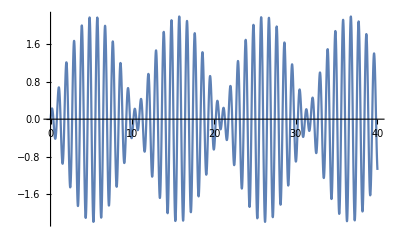

A2 = 2.0

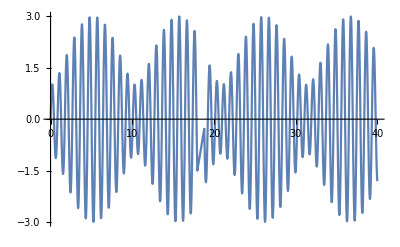

A2 = 5.0

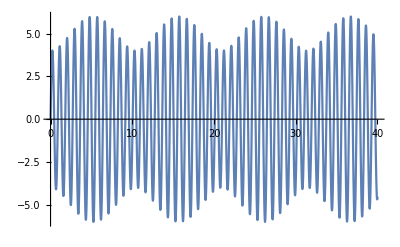

A2 = 6.0

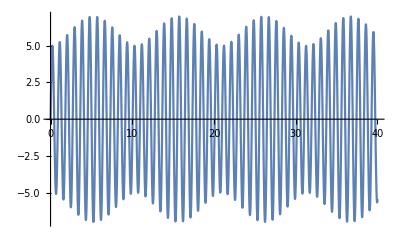

```mathematica
(*Problem 2 Part ii*)
Remove["Global`*"]
(*eqations*)
y[1][x_,t_]=A1 Sin[k1 (x-v t)];
y[2][x_,t_]=A2 Sin[k2 (x+v t)];
y[r][x_,t_]=y[1][x,t]+y[2][x,t];
(*plug in variables*)
k2=k1+δk;
v=1;
k1=2 π;
A1=1;
δk=.6;
Print["A2 = 1.2"]
Plot[y[r][0,t]/.A2->1.2,{t,0,40}]
Print["A2 = 2.0"]
Plot[y[r][0,t]/.A2->2.0,{t,0,40}]
Print["A2 = 5.0"]
Plot[y[r][0,t]/.A2->5.0,{t,0,40}]
Print["A2 = 6.0"]
Plot[y[r][0,t]/.A2->6.0,{t,0,40}]
```

```mathematica
(*Problem 2 Part iii*)
Remove["Global`*"]
(*eqations*)
y[1][x_,t_]=A1 Sin[k1 (x-v t)];
y[2][x_,t_]=A2 Sin[k2 (x+v t)];
y[r][x_,t_]=y[1][x,t]+y[2][x,t];
(*plug in variables*)
k2=k1+δk;
v=1;
k1=2 π;
A1=1;
A2=2;
δk=0.5;
(*Plot and Animate*)
waveplot[t_]:= Plot[y[r][x,t],{x,0,20},PlotStyle->Black]
Animate[waveplot[t],{t,0,50, 0.1}]
```

```mathematica
(*Problem 3*)
Remove["Global`*"]
SetAttributes[{k0,ω0,δk,ω0p},Constant];
$Assumptions={Element[{k0,ω0,δk,ω0p,t},Reals] && k0>0 && ω0>0 && δk >0};
case=3;
If[case==1, A[k_]=1];
If[case==2, A[k_]=DiracDelta[k-k0]];If[case==3,A[k_]=Cos[π (k-k0)/2/δk]];
If[case==4,A[k_]=(k-k0+δk/2)/δk];
If[case==5,A[k_]=(k-k0)^2/(δk/2)^2];
klo=k0-δk;
khi=k0+δk;
ω = ω0 + ω0p (k-k0);
Ψ[x_,t_]=Integrate[ A[k] E^(I (ω t - k x)),{k,klo,khi}]//Simplify;
Print["\n\nΨ[x,t] = ",Ψ[x,t]]
SuperStar[z_] :=Conjugate[z];
Θ[x_,t_]=1/2 (Ψ[x,t] + SuperStar[Ψ[x,t]]);
k0 = 2 π;
δk =  0.1 π;
ω0 = 0.2 π;
ω0p = 0.3 π;
amplot:=Plot[A[k],{k,klo,khi},PlotRange->{{klo-δk, khi+δk},{-1,3}},AxesLabel->{"k","A[k]"}];
xx = 75;
yy=2.4;
range={{-xx,xx},{-yy,yy}};
Animate[Plot[Θ[x,t],{x,-xx,xx},PlotRange->range],{t,-100,100}]
```

Ψ[x,t] = (4 ⅇ^(-ⅈ k0 x+ⅈ t ω0) π δk Cos[δk (x-t ω0p)])/((π-2 x δk+2 t δk ω0p) (π+2 δk (x-t ω0p)))

If[debug,Print[
b_n = ,b[n]]]

At t=0, the displaced medium looks like:

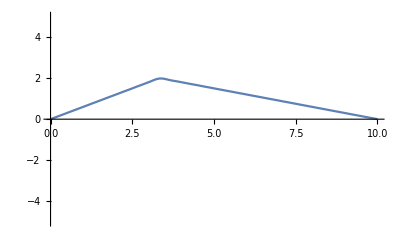

```mathematica
(*Problem 4*)
Remove["Global`*"]
SetAttributes[{a,f,L},Constant];
$Assumptions={Element[{a,f,L,x},Reals] && Element[n,Integers]&& a > 0 && 0≤ f ≤ 1 && L > 0 && 0 ≤ x ≤ L  };
npieces =2;
f[1][x_]= a  x/(f L);
xlo[1]=0;
xhi[1]= f L;

f[2][x_]=a - a (x-f L)/(L - f L);
xlo[2]=xhi[1];
xhi[2]= L;
b[n_]= 2/L Sum[Integrate[f[i][x] Sin[n π x/L],{x,xlo[i],xhi[i]}],{i,1,npieces}]//Refine//Simplify;
L=10;
f = 1/3;
a=2;
vx=1;
nterms = 40;
xlow = xlo[1];
xhigh=xhi[npieces];
yrange=5;
range={{xlow,xhigh},{-yrange,yrange}};
blist=Table[{n,b[n]},{n,1,nterms}];
wave[x_,t_]=Sum[b[n] Sin[n π x/L] Cos[n π vx/L t],{n,1,nterms}];
vtrans[x_,t_] = D[wave[x,t],t];
Print["\nAt t=0, the displaced medium looks like:"]
Plot[wave[x,0],{x,xlow,xhigh},PlotRange->range]
waveplot[t_]:= Plot[{wave[x,t],vtrans[x,t]},{x,xlow,xhigh},PlotRange->range,PlotStyle->{Red,Blue}]
Animate[waveplot[t],{t,0,50, 0.2},DisplayAllSteps->True]
```

```mathematica
(*Problem 5 Part i*)
Remove["Global`*"]
$Assumptions={Element[{ϕ0,α},Reals] && ϕ0 > 0 && α>0};
ϕ[α_,x_] = ϕ0 E^(-α x^2);
c[α_,k_] = FourierTransform[ϕ[α,x],x,k]//FullSimplify;
Print["\nϕ[x] = ",ϕ[α,x]]
Print["c[k] = ",c[α,k]]
ϕ0 = 5;
xrange={{-10,10},{0,1.2 ϕ0}};
krange={{-8,8},{0,20}};
plotϕ[α_] := Plot[ϕ[α,x],{x,-5 α,5 α},PlotRange->xrange,PlotLabel->"ϕ[x]" ,PlotStyle->Red]
plotc[α_] := Plot[c[α,k],{k,-20,20},PlotRange->krange,PlotLabel->"c[k]",PlotStyle->Red]
pix[α_]:=GraphicsGrid[{{plotϕ[α],plotc[α]}}] 
Manipulate[pix[α],{α,0.4,5.0}]
```

ϕ[x] = ⅇ^(-x^2 α) ϕ0

c[k] = (ⅇ^(-k^2/(4 α)) ϕ0)/(√2 √α)

1

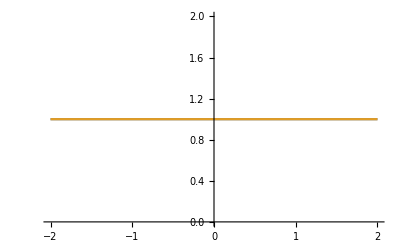

```mathematica
(*Problem 5 Part ii*)
Remove["Global`*"]
f[x_]=1;
SetAttributes[L,Constant];
$Assumptions={Element[L,Reals] &&L>0};
a0=1/L Integrate[f[x],{x,-L,L}];
a[n_]=2/L Integrate[f[x] Cos[n π x /L],{x,-L,L}];
b[n_]= 2/L Integrate[f[x] Sin[n π x/L],{x,-L,L}];
L=1;
F[x_]=a0/2+Sum[a[n]+b[n],{n,1,10}];
Plot[{f[x],F[x]},{x,-2,2}]
```

```mathematica
(*Problem 6*)
Remove["Global`*"]
$Assumptions={Element[{A,ω0,ω,t},Reals] && A>0 && ω0>0 && ω>0};
F1[t_] = A Sin[ω0 t];
c1[ω_] = FourierTransform[F1[t],t,ω]//Simplify;
Print["c[ω] = ",c1[ω]]
F2[t_] =  A Sin[ω1 t]  Sin[ω2 t];
c2[ω_] = FourierTransform[F2[t],t,ω]//Simplify;
Print["c[ω] = ",c2[ω]]
A[k_]=Cos[π (k-k0)/2/δk];
klo=k0-δk;
khi=k0+δk;
ω = ω0 + ω0p (k-k0);
Ψ[x_,t_]=Integrate[ A[k] E^(I (ω t - k x)),{k,klo,khi}]//Simplify;
c3[ω_] = FourierTransform[Ψ[x,0],x,ω]//Simplify;
Print["c[ω] = ",c3[ω]]
```

The spectral decomposition of a monotonic wave of frequency ω0 is:

c[ω] = ⅈ A √(π/2) DiracDelta[ω-ω0]

The spectral decomposition of the amplitude modulated wave is:

c[ω] = -1/2 A √(π/2) DiracDelta[ω-ω1-ω2]+1/2 A √(π/2) DiracDelta[ω+ω1-ω2]+1/2 A √(π/2) DiracDelta[ω-ω1+ω2]-1/2 A √(π/2) DiracDelta[ω+ω1+ω2]

c[ω] = 1/2 ⅈ √(π/2) ((-ⅈ Cos[(π (k0-ω0-k ω0p+k0 ω0p))/(2 δk)]+Cos[(π (k0+δk-ω0-k ω0p+k0 ω0p))/(2 δk)]) (-2 Cos[(π (k0-ω0-k ω0p+k0 ω0p))/(2 δk)] (Cos[(π (k0-ω0-k ω0p+k0 ω0p))/(2 δk)]-ⅈ Cos[(π (k0+δk-ω0-k ω0p+k0 ω0p))/(2 δk)]) Sign[k0+δk-ω0-k ω0p+k0 ω0p] (-1+Sign[Abs[Im[1/δk]]])-2 Sign[Im[1/δk]] (HeavisideTheta[-(k0+δk-ω0-k ω0p+k0 ω0p) Sign[Im[1/δk]]]+HeavisideTheta[(k0+δk-ω0-k ω0p+k0 ω0p) Sign[Im[1/δk]]] (Cos[(π (k0+δk-ω0-k ω0p+k0 ω0p))/δk]+ⅈ Sin[(π (k0+δk-ω0-k ω0p+k0 ω0p))/δk])))+(-ⅈ Cos[(π (k0-ω0-k ω0p+k0 ω0p))/(2 δk)]+Sin[(π (k0-ω0-k ω0p+k0 ω0p))/(2 δk)]) (-2 Sign[δk+ω0+k ω0p-k0 (1+ω0p)] (-1+Sign[Abs[Im[1/δk]]]) Sin[(π (δk+ω0+k ω0p-k0 (1+ω0p)))/(2 δk)] (-ⅈ Cos[(π (δk+ω0+k ω0p-k0 (1+ω0p)))/(2 δk)]+Sin[(π (δk+ω0+k ω0p-k0 (1+ω0p)))/(2 δk)])-2 Sign[Im[1/δk]] (HeavisideTheta[-(δk+ω0+k ω0p-k0 (1+ω0p)) Sign[Im[1/δk]]]+HeavisideTheta[(δk+ω0+k ω0p-k0 (1+ω0p)) Sign[Im[1/δk]]] (Cos[(π (δk+ω0+k ω0p-k0 (1+ω0p)))/δk]+ⅈ Sin[(π (δk+ω0+k ω0p-k0 (1+ω0p)))/δk]))))